```mathematica
(* Global Representation Space (GRS) ; 
   θY A p Subscript[y, 0] d lnum ;       
   1  2 3 4  5  6  ; *)
```

```mathematica
zero[p_?NumberQ,y0_?NumberQ,dnum_?NumberQ,Lnum_?NumberQ]:=Block[
{sol,s,y,a,x,θ},
sol=NDSolve[
{y'[s]==Sin[θ[s]],
x'[s]==Cos[θ[s]],
a'[s]==(-2*y[s])*Cos[θ[s]],
θ'[s]==p-y[s],

a[0]==0,
x[0]== 0,
θ[0]== 0,
y[0]==y0},

{y[s],a[s],θ[s],x[s]},{s,0,Lnum}
];

(*conditions de bords*)
{y[s],a[s]-A,θ[s]-θY,x[s] - dnum}/.sol[[1]]/.s->Lnum
]
```

```mathematica
θY=0.1
grsdepart={0.1,0.009999999999999995,0.24639304723812214,-0.01950401837144732,0.38490754943459693,0.38556282762390204};
listeGRS={grsdepart}; 
dernierpointtrouve=listeGRS[[-1]];
A=dernierpointtrouve[[2]];
{papprox,y0approx,dapprox,Lapprox}=grsdepart[[{3,4,5,6}]];
(* c'est la matrice de sortie *)
```

0.1

```mathematica
zero[papprox,y0approx,dapprox,Lapprox]
```

{-7.71427×10^-11,-0.0000102533,7.52295×10^-11,1.03705×10^-11}

```mathematica
fr=FindRoot[zero[p,y0,dnum,Lnum],{p,papprox},{y0,y0approx},{dnum,dapprox},{Lnum,Lapprox},
MaxIterations->30,
Jacobian->"FiniteDifference",
Method->{"Newton", "UpdateJacobian"->1}];
```

```mathematica
Print[{p,y0,dnum,Lnum}/.fr];
```

{0.246255,-0.0195142,0.385103,0.385759}

fonction du tir1

```mathematica
θY=0.1;
tailledupas=0.05;
imax=300;
grsdepart={0.1,0.009999999999999995,0.24639304723812214,-0.01950401837144732,0.38490754943459693,0.38556282762390204};
listeGRS={grsdepart}; 
{papprox,y0approx,dapprox,Lapprox}=grsdepart[[{3,4,5,6}]];
A=grsdepart[[2]]+ + tailledupas;
fr=FindRoot[zero[p,y0,dnum,Lnum],{p,papprox},{y0,y0approx},{dnum,dapprox},{Lnum,Lapprox},
MaxIterations->30,
Jacobian->"FiniteDifference",
Method->{"Newton", "UpdateJacobian"->1}];

(* je verifie si c est une bonne solution *)
erreur=Total[Abs[zero[p/.fr,y0/.fr,dnum/.fr,Lnum/.fr]]];
(* θY  A  q  Subscript[y, 0] d lgc ;   
    1  2  3  4  5  6  ; *)
AppendTo[listeGRS,{θY,A,p,y0,dnum,Lnum}/.fr];
Print[erreur];
LastPtFind=listeGRS[[-1]];
Last2PtFind=listeGRS[[-2]];
Print["Last2PtFind : ",Last2PtFind];
Print["LastPtFind : ",LastPtFind];
```

4.2588×10^-16

Last2PtFind : {0.1,0.01,0.246393,-0.019504,0.384908,0.385563}

LastPtFind : {0.1,0.06,0.075902,-0.0496081,0.920047,0.92178}

zero2 (s)

```mathematica
zero2[A_?NumberQ,p_?NumberQ,y0_?NumberQ,dnum_?NumberQ,Lnum_?NumberQ]:=Block[
{sol,s,y,a,x,θ},
sol=NDSolve[
{y'[s]==Sin[θ[s]],
x'[s]==Cos[θ[s]],
a'[s]==(-2*y[s])*Cos[θ[s]],
θ'[s]==p-y[s],

a[0]==0,
x[0]== 0,
θ[0]== 0,
y[0]==y0},

{y[s],a[s],θ[s],x[s]},{s,0,Lnum}
];

(*conditions de bords*)
{y[s],a[s]-A,θ[s]-θY,x[s] - dnum,
u.{(A - Aapprox),(p - papprox),(y0 - y0approx),(dnum - dapprox),(Lnum - Lapprox)}}/.sol[[1]]/.s->Lnum
]
```

```mathematica
Testcase
(* Global Representation Space (GRS) ; 
   θY A p Subscript[y, 0] d lnum ;       
   1  2 3 4  5  6  ; *)
```

```mathematica
AAV=LastPtFind[[2]];
pAV=LastPtFind[[3]];
y0AV=LastPtFind[[4]];
dAV=LastPtFind[[5]];
LAV=LastPtFind[[6]];

AAV2=Last2PtFind[[2]];
pAV2=Last2PtFind[[3]];
y0AV2=Last2PtFind[[4]];
dAV2=Last2PtFind[[5]];
LAV2=Last2PtFind[[6]];
tailledupas=0.1;
u=Normalize[{AAV-AAV2,pAV-pAV2,y0AV-y0AV2,dAV-dAV2,LAV-LAV2}];
{Aapprox,papprox,y0approx,dapprox,Lapprox}={AAV,pAV,y0AV,dAV,LAV}+u*tailledupas;
Print[Aapprox,"/",papprox,"/",y0approx,"/",dapprox,"/",Lapprox];
Print[u]
```

0.0664268/0.0540776/-0.053442/0.988262/0.990132

{0.0642684,-0.219041,-0.0386543,0.687202,0.688586}

```mathematica
fr2=FindRoot[zero2[A,p,y0,dnum,Lnum],{A,Aapprox},{p,papprox},{y0,y0approx},{dnum,dapprox},{Lnum,Lapprox},
MaxIterations->30,
Jacobian->"FiniteDifference",
Method->{"Newton", "UpdateJacobian"->1}];
```

```mathematica
erreur=Total[Abs[zero2[A/.fr2, p/.fr2, y0/.fr2, dnum/.fr2,Lnum/.fr2]]];
Which[
erreur<10^-6,
(* θY  A  q  Subscript[y, 0] d Bo ;   
    1  2  3  4  5  6  ; *)
AppendTo[listeGRS,{θY,A,p,y0,dnum,Lnum}/.fr2];
,
erreur≥10^-6,
Print[erreur];
]
LastPtFind=listeGRS[[-1]];
Last2PtFind=listeGRS[[-2]];
Print["Last2PtFind : ",Last2PtFind];
Print["LastPtFind : ",LastPtFind];
```

Last2PtFind : {0.1,0.06,0.0759817,-0.0495766,0.919542,0.921274}

LastPtFind : {0.1,0.0702383,0.0654199,-0.0540432,0.989856,0.99176}

Fonction du tir mieux

```mathematica
Do[
{AAV,pAV,y0AV,dAV,LAV}=LastPtFind[[{2,3,4,5,6}]];
{AAV2,pAV2,y0AV2,dAV2,LAV2}=Last2PtFind[[{2,3,4,5,6}]];
u=Normalize[{AAV-AAV2,pAV-pAV2,y0AV-y0AV2,dAV-dAV2,LAV-LAV2}];
(*Print["u:",u];*)

Label[begin];
{Aapprox,papprox,y0approx,dapprox,Lapprox}={AAV,pAV,y0AV,dAV,LAV}+u*tailledupas;
(*Print["previous:",{Vapprox,papprox,z0approx,dapprox}];*)

fr2=FindRoot[zero2[A,p,y0,dnum,Lnum],{A,Aapprox},{p,papprox},{y0,y0approx},{dnum,dapprox},{Lnum,Lapprox},
MaxIterations->30,
Jacobian->"FiniteDifference",
Method->{"Newton", "UpdateJacobian"->1}];

(* je verifie si c est une bonne solution *)
erreur=Total[Abs[zero2[A/.fr2, p/.fr2, y0/.fr2, dnum/.fr2,Lnum/.fr2]]];

Which[
erreur<10^-6,
AppendTo[listeGRS,{θY,A,p,y0,dnum,Lnum}/.fr2];
LastPtFind=listeGRS[[-1]];
Last2PtFind=listeGRS[[-2]];
(*Print["LastPtFind:",{V2,p,z0,d}/.fr];*)
,

erreur≥10^-6,
(* did not converge : probleme*)
tailledupas=tailledupas*0.8;
If[tailledupas<10^-6,Print["Stop !!!"];Abort[]];
Print[i," erreur = ",erreur," nouvelle taille du pas : ",tailledupas];
Goto[begin]
,

True,Print["Je ne comprends pas erreur : ",erreur]
];

If[Mod[i,50]==0,
Print[i,"/",imax];
]
,{i,1,imax}]
```

50/300

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

100/300

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

150/300

200/300

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

250/300

300/300

```mathematica
(* Global Representation Space (GRS) ; 
   θY A p Subscript[y, 0] d lnum ;       
   1  2 3 4  5  6  ; *)
data=Abs[listeGRS[[All,{2,5}]]];
```

```mathematica
(*save data for further use*)
DeleteFile[NotebookDirectory[]<>"2dpinning.data"];
Save[NotebookDirectory[]<>"2dpinning.data",{
listeGRS
}];
Print[FileByteCount[(NotebookDirectory[]<>"2dpinning.data")]/1024/1024.," Mo"]
```

0.0348473 Mo

```mathematica
(*get data from .data*)
Get[(NotebookDirectory[]<>"2dpinning.data")];
```

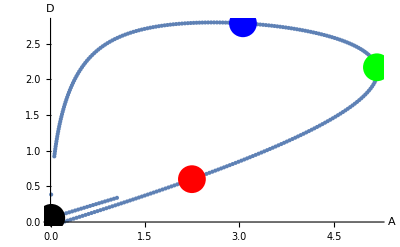

```mathematica
plotnumerique=ListPlot[data,AxesLabel-> {Style["A",FontSize->22],Style["D",FontSize->22]},LabelStyle->{FontSize->22},AspectRatio->1/GoldenRatio,AxesStyle->Black];
Datadots=data[[{100,155,232,280}]];
plotdot2=ListPlot[Datadots,Epilog->{PointSize[0.05],Riffle[{Blue,Green,Red,Black},Point/@Datadots]}];
Show[plotnumerique,plotdot2,AxesStyle->Black,Epilog->{PointSize[0.05],Riffle[{Blue,Green,Red,Black},Point/@Datadots]}]
```

gif

```mathematica
data2Dsliding=listeGRS[[All]];
iplot2Dmax=Length[data2Dsliding]
Do[
listplot2Dsliding=data2Dsliding[[j]];
{Aplot,pplot,y0plot,dplot,Lplot}=listplot2Dsliding[[{2,3,4,5,6}]];
solforme=NDSolve[{
θ'[s]==pplot-y[s],
y'[s]==Sin[θ[s]],
x'[s]==Cos[θ[s]],
a'[s]== - 2*y[s]*Cos[θ[s]],

a[0]==0,
θ[0]== 0,
y[0]== y0plot,
x[0]==0},{y,a,x,θ},{s,0,Lplot}
][[1]];
splot2Dsliding[j]=ParametricPlot[{x[s],y[s]}/.solforme,{s,0,Lplot},AxesLabel-> {Style["x",FontSize->22],Style["y",FontSize->22]},LabelStyle->{FontSize->22},AspectRatio->1/GoldenRatio,PlotRange->{{-3,3},{-4,0}},AxesStyle->Black];
,
{j,1,iplot2Dmax}];
```

```mathematica
Manipulate[Show[splot2Dsliding[i]],{i,1,iplot2Dmax,1}]
```

```mathematica
gif=Animate[splot2Dsliding[i],{i,1,iplot2Dmax,2}];
```

```mathematica
Export["2Dsliding.gif",gif]
```

2Dsliding.gif

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["2Dsliding.gif"]]]
```

c’est le plot

```mathematica
Clear[splot,splot2]
positiondots={100,155,232,280};
j=1;
Color={Blue,Green,Red,Black};
Do[
number=positiondots[[j]];
listplot=listeGRS[[number]];
{Aplot,pplot,y0plot,dplot,Lplot}=listplot[[{2,3,4,5,6}]];
Print["plot:",Aplot,"/",pplot,"/",y0plot,"/",dplot,"/",Lplot,"/",Color[[j]],"/",number];
solforme=NDSolve[{
θ'[s]==pplot-y[s],
y'[s]==Sin[θ[s]],
x'[s]==Cos[θ[s]],
a'[s]== - 2*y[s]*Cos[θ[s]],

a[0]==0,
θ[0]== 0,
y[0]== y0plot,
x[0]==0},{y,a,x,θ},{s,0,Lplot}
][[1]];
splot[j]=ParametricPlot[{x[s],y[s]}/.solforme,{s,0,Lplot},AxesLabel-> {Style["x",FontSize->22],Style["y",FontSize->22]},LabelStyle->{FontSize->22},AspectRatio->1/GoldenRatio,PlotRange->{{-3,3},{-4,0}},AxesStyle->Black,PlotStyle->Color[[j]]];
splot2[j]=ParametricPlot[{-x[s],y[s]}/.solforme,{s,0,Lplot},AxesLabel-> {Style["r",FontSize->22],Style["z",FontSize->22]},LabelStyle->{FontSize->22},AspectRatio->1/GoldenRatio,PlotRange->{{-3,3},{-4,0}},AxesStyle->Black,PlotStyle->Color[[j]]];
,
{j,1,4}]
```

plot:3.05668/-0.512942/0/2.78493/3.00484/RGBColor[0, 0, 1]/100

plot:5.18459/-1.14943/0/2.16844/3.38039/RGBColor[0, 1, 0]/155

plot:2.24572/-1.70402/0/0.600361/4.18044/RGBColor[1, 0, 0]/232

plot:-0.0115051/-1.81551/0/-0.0581579/4.58918/GrayLevel[0]/280

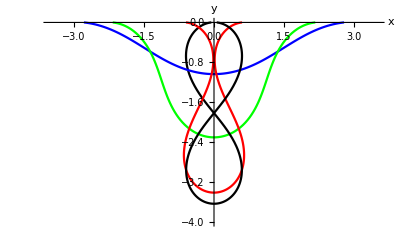

```mathematica
tb3D=Table[splot[i],{i,1,4,1}];
tb3D2=Table[splot2[i],{i,1,4,1}];
Show[tb3D,tb3D2,PlotRange->{{-3.5,3.5},{-4,0}}]
```

c’est les donnes calcul avant 2D bvp

```mathematica
Data2={{0.07170979026585593,1},{0.07404872721167832,1.015},{0.07723932998863377,1.035},{0.08051374130990673,1.055},{0.08387351162545238,1.075},{0.08732027177949683,1.095},{0.09085571682405541,1.115},{0.09448161483821133,1.135},{0.09819980990475173,1.155},{0.10201222516476022,1.175},{0.10592087495760096,1.195},{0.10992784115238946,1.215},{0.1140353220814482,1.235},{0.11824559977600776,1.2550000000000001},{0.12256106205597718,1.2750000000000001},{0.1269842037814771,1.2950000000000002},{0.13151763345486,1.3150000000000002},{0.13616407926708038,1.3350000000000002},{0.14092639532253315,1.3550000000000002},{0.1458075698564006,1.3750000000000002},{0.15081073156051242,1.3950000000000002},{0.15593915661860372,1.4150000000000003},{0.16119628486534554,1.4350000000000003},{0.16658571878318118,1.4550000000000003},{0.17211123800404768,1.4750000000000003},{0.17777681119151034,1.4950000000000003},{0.18358660685527772,1.5150000000000003},{0.18954500597906715,1.5350000000000004},{0.1956566151753853,1.5550000000000004},{0.2019262836079413,1.5750000000000004},{0.20835910788979967,1.5950000000000004},{0.21496046832731436,1.6150000000000004},{0.22173603373655962,1.6350000000000005},{0.2286917837926588,1.6550000000000005},{0.23583403247728646,1.6750000000000005},{0.2431694508301444,1.6950000000000005},{0.2507050966027984,1.7150000000000005},{0.25844842989939965,1.7350000000000005},{0.26640735937800686,1.7550000000000006},{0.27459026690940186,1.7750000000000006},{0.28300604596470536,1.7950000000000006},{0.2916641436632873,1.8150000000000006},{0.30057460070144976,1.8350000000000006},{0.30974810164581573,1.8550000000000006},{0.31919602957236914,1.8750000000000007},{0.3289305259866179,1.8950000000000007},{0.33896454913139334,1.9150000000000007},{0.3493119532909585,1.9350000000000007},{0.3599875639463652,1.9550000000000007},{0.37100725509995064,1.9750000000000008},{0.3823880059761698,1.9950000000000008},{0.39414832824299795,2.0150000000000006},{0.4063078120919016,2.0350000000000006},{0.4188877487006575,2.0550000000000006},{0.4319110607923335,2.0750000000000006},{0.44540255045502397,2.0950000000000006},{0.45938909046996584,2.1150000000000007},{0.47389984491538156,2.1350000000000007},{0.48896653992685035,2.1550000000000007},{0.504623725953903,2.1750000000000007},{0.5209091548121526,2.1950000000000007},{0.5378641466277155,2.2150000000000007},{0.5555340690239348,2.2350000000000008},{0.5739688062982905,2.255000000000001},{0.5932234173875229,2.275000000000001},{0.6133588715069126,2.295000000000001},{0.6333588715069126,2.313994200969977},{0.6533588715069126,2.3321713606053036},{0.6733588715069126,2.3495783432123543},{0.6933588715069127,2.3662586003896067},{0.7133588715069127,2.382252385501087},{0.7333588715069127,2.397597043686663},{0.7533588715069127,2.4123272684256056},{0.7733588715069127,2.4264753354848825},{0.7933588715069128,2.440071289372867},{0.8133588715069128,2.45314318710407},{0.8333588715069128,2.465717201530251},{0.8533588715069128,2.4778178031487057},{0.8733588715069128,2.4894678801872696},{0.8933588715069128,2.5006888854758165},{0.9133588715069129,2.511500925600674},{0.9333588715069129,2.5219228705211565},{0.9533588715069129,2.5319724447192646},{0.9733588715069129,2.54166630375777},{0.9933588715069129,2.5510201296311688},{1.0133588715069128,2.5600486834940677},{1.0333588715069129,2.5687658765428822},{1.0533588715069129,2.577184828218208},{1.073358871506913,2.585317917782902},{1.093358871506913,2.5931768383013685},{1.113358871506913,2.600772641995404},{1.133358871506913,2.6081157799519867},{1.153358871506913,2.615216142403471},{1.173358871506913,2.622083094789243},{1.193358871506913,2.6287255084838654},{1.213358871506913,2.6351517969178833},{1.233358871506913,2.641369940773105},{1.253358871506913,2.6473875146667973},{1.273358871506913,2.6532117121028462},{1.293358871506913,2.6588493687712447},{1.313358871506913,2.6643069804811956},{1.3333588715069131,2.6695907289862184},{1.3533588715069131,2.674706495981461},{1.3733588715069132,2.6796598814333095},{1.3933588715069132,2.684456219599397},{1.4133588715069132,2.689100596142759},{1.4333588715069132,2.6935978538713754},{1.4533588715069132,2.6979526170438235},{1.4733588715069132,2.7021692967322677},{1.4933588715069133,2.7062521037918827},{1.5133588715069133,2.7102050642816544},{1.5333588715069133,2.7140320139219414},{1.5533588715069133,2.7177366268634446},{1.5733588715069133,2.7213224136226692},{1.5933588715069134,2.724792735119945},{1.6133588715069134,2.728150800736384},{1.6333588715069134,2.7313996858289555},{1.6533588715069134,2.734542333859357},{1.6733588715069134,2.737581515297785},{1.6933588715069134,2.7405200313415237},{1.7133588715069135,2.743360418934689},{1.7333588715069135,2.746105158724212},{1.7533588715069135,2.7487566291499443},{1.7733588715069135,2.75131711121336},{1.7933588715069135,2.753788793009682},{1.8133588715069135,2.7561737740053918},{1.8333588715069136,2.7584740690748544},{1.8533588715069136,2.7606916123210796},{1.8733588715069136,2.7628282606769354},{1.8933588715069136,2.7648857975850514},{1.9133588715069136,2.766865935632239},{1.9333588715069137,2.768770319981062},{1.9533588715069137,2.7706005312749613},{1.9733588715069137,2.7723581183987163},{1.9933588715069137,2.7740444814242093},{2.0133588715069135,2.7756610482847974},{2.0333588715069135,2.777209175946035},{2.0533588715069135,2.778690156215921},{2.0733588715069136,2.780105235019807},{2.0933588715069136,2.7814556101205046},{2.1133588715069136,2.782742419055043},{2.1333588715069136,2.783966791630241},{2.1533588715069136,2.7851297856464883},{2.1733588715069136,2.78623242270666},{2.1933588715069137,2.787275681386065},{2.2133588715069137,2.788260515322652},{2.2333588715069137,2.7891878276319972},{2.2533588715069137,2.790058493270101},{2.2733588715069137,2.7908733499513754},{2.2933588715069138,2.7916332032732774},{2.3133588715069138,2.792338838299602},{2.333358871506914,2.7929909784519986},{2.353358871506914,2.7935903550699224},{2.373358871506914,2.7941376346449043},{2.393358871506914,2.7946334836265185},{2.413358871506914,2.795078530776014},{2.433358871506914,2.7954733794664564},{2.453358871506914,2.7958186220427566},{2.473358871506914,2.7961147830076998},{2.493358871506914,2.7963623832501576},{2.513358871506914,2.7965619726603363},{2.533358871506914,2.796714026049496},{2.553358871506914,2.7968189815341855},{2.573358871506914,2.7968772902484647},{2.593358871506914,2.796889371365459},{2.613358871506914,2.796855623848503},{2.633358871506914,2.7967764264188744},{2.653358871506914,2.7966521387381578},{2.673358871506914,2.7964831010368623},{2.693358871506914,2.7962696354156873},{2.713358871506914,2.7960120456601523},{2.733358871506914,2.795710617706763},{2.753358871506914,2.7953656200077384},{2.773358871506914,2.7949772961759622},{2.793358871506914,2.794545895110406},{2.813358871506914,2.794071627307462},{2.8333588715069142,2.793554699325867},{2.8533588715069143,2.7929952867305605},{2.8733588715069143,2.7923935635637798},{2.8933588715069143,2.79174968314998},{2.9133588715069143,2.791063774623968},{2.9333588715069143,2.790335984445784},{2.9533588715069143,2.7895663992556052},{2.9733588715069144,2.788755117331521},{2.9933588715069144,2.787902215968572},{3.0133588715069144,2.787007756698573},{3.0333588715069144,2.7860717775839388},{3.0533588715069144,2.78509433794279},{3.0733588715069144,2.784075431199217},{3.0933588715069145,2.7830150674986216},{3.1133588715069145,2.781913234959878},{3.1333588715069145,2.7807699058307094},{3.1533588715069145,2.7795850384225993},{3.1733588715069145,2.778358575250254},{3.1933588715069146,2.7770904476927307},{3.2133588715069146,2.7757805671049263},{3.2333588715069146,2.77442883142229},{3.2533588715069146,2.7730351216136353},{3.2733588715069146,2.7715993058192723},{3.2933588715069146,2.770121232166986},{3.3133588715069147,2.768600740263968},{3.3333588715069147,2.767037646726918},{3.3533588715069147,2.7654317532427366},{3.3733588715069147,2.763782845545746},{3.3933588715069147,2.7620906920243593},{3.4133588715069147,2.7603550436687665},{3.4333588715069148,2.7585756218094906},{3.453358871506915,2.756752164543758},{3.473358871506915,2.7548843570528763},{3.493358871506915,2.7529718847864295},{3.513358871506915,2.7510143881058475},{3.533358871506915,2.74901151341585},{3.553358871506915,2.7469628776196755},{3.573358871506915,2.744868061861113},{3.593358871506915,2.7427266805967827},{3.613358871506915,2.740538246885324},{3.633358871506915,2.7383023024894015},{3.653358871506915,2.7360183470793795},{3.673358871506915,2.733685861310772},{3.693358871506915,2.7313042980527587},{3.713358871506915,2.728873082129421},{3.733358871506915,2.7263916105878274},{3.753358871506915,2.723859254978191},{3.773358871506915,2.721275352439527},{3.793358871506915,2.718639209999645},{3.813358871506915,2.7159500938613306},{3.833358871506915,2.713207266439175},{3.853358871506915,2.7104099261275985},{3.873358871506915,2.707557215275546},{3.893358871506915,2.7046482757976884},{3.913358871506915,2.7016821977684495},{3.933358871506915,2.6986580238866242},{3.9533588715069152,2.6955747378663184},{3.9733588715069152,2.6924312969489677},{3.9933588715069153,2.6892266009733254},{4.013358871506915,2.6859594684625123},{4.033358871506914,2.6826287285128387},{4.053358871506914,2.6792330981520065},{4.073358871506914,2.6757712443106665},{4.093358871506913,2.6722417725065957},{4.113358871506913,2.668643188695402},{4.133358871506912,2.6649739584124834},{4.153358871506912,2.6612324552060467},{4.173358871506911,2.657416960403532},{4.193358871506911,2.653525682849145},{4.213358871506911,2.6495567243517617},{4.23335887150691,2.6455080630750456},{4.25335887150691,2.641377590208307},{4.273358871506909,2.637163078357745},{4.293358871506909,2.6328621509060155},{4.313358871506908,2.6284722882792773},{4.333358871506908,2.623990874129949},{4.353358871506908,2.6194150785273904},{4.373358871506907,2.6147419085671113},{4.393358871506907,2.6099681241446815},{4.413358871506906,2.6050904577123473},{4.433358871506906,2.600105241733943},{4.4533588715069055,2.5950086177429186},{4.473358871506905,2.5897964577563344},{4.493358871506905,2.5844643435800356},{4.513358871506904,2.579007531259173},{4.533358871506904,2.5734209299854918},{4.553358871506903,2.567699008287401},{4.573358871506903,2.561835843509067},{4.5933588715069025,2.5558250048105853},{4.613358871506902,2.549659518152389},{4.633358871506902,2.5433317963382964},{4.653358871506901,2.5368335529420896},{4.673358871506901,2.5301557253590703},{4.6933588715069,2.5232883660942163},{4.7133588715069,2.5162205155360295},{4.7333588715068995,2.5089400419904173},{4.753358871506899,2.501433510350899},{4.773358871506899,2.493685850399865},{4.793358871506898,2.485680286043829},{4.813358871506898,2.4773977673881977},{4.833358871506897,2.4688168534362402},{4.853358871506897,2.4599129191383566},{4.8733588715068965,2.450657760673192},{4.893358871506896,2.4410186123245805},{4.913358871506896,2.4309571804901857},{4.933358871506895,2.4204281730576955},{4.953358871506895,2.4093773611233287},{4.973358871506894,2.3977390199731796},{4.993358871506894,2.3854318506604266},{5.0133588715068935,2.372353847896474},{5.033358871506893,2.3583735636007135},{5.053358871506893,2.343316835126038},{5.073358871506892,2.3269444012201106},{5.093358871506892,2.308911612835741},{5.113358871506891,2.2886890903584267},{5.130717183711759,2.2686890903584267},{5.145762230942172,2.2486890903584267},{5.158585013585046,2.2286890903584267},{5.169269142468873,2.2086890903584266},{5.177891244856088,2.1886890903584266},{5.184523555530715,2.1686890903584266},{5.189232519425746,2.1486890903584266},{5.192081059891716,2.1286890903584266},{5.19312877018582,2.1086890903584266},{5.192431363405754,2.0886890903584265},{5.19004157055755,2.0686890903584265},{5.1860085708868535,2.0486890903584265},{5.180379869639352,2.0286890903584265},{5.173199377831315,2.0086890903584265},{5.164510236673747,1.9886890903584264},{5.154352011131382,1.9686890903584264},{5.142763463516675,1.9486890903584264},{5.129781074756274,1.9286890903584264},{5.115439933755723,1.9086890903584264},{5.099773398774914,1.8886890903584264},{5.082813669654123,1.8686890903584263},{5.064591478688171,1.8486890903584263},{5.045136397465665,1.8286890903584263},{5.024476311067652,1.8086890903584263},{5.002639079352178,1.7886890903584263},{4.979650746207952,1.7686890903584263},{4.955536600523972,1.7486890903584262},{4.930321091065905,1.7286890903584262},{4.904027860991364,1.7086890903584262},{4.8766795111542685,1.6886890903584262},{4.848298232174027,1.6686890903584262}}
```

{{0.0717098,1},{0.0740487,1.015},{0.0772393,1.035},{0.0805137,1.055},{0.0838735,1.075},{0.0873203,1.095},{0.0908557,1.115},{0.0944816,1.135},{0.0981998,1.155},{0.102012,1.175},{0.105921,1.195},{0.109928,1.215},{0.114035,1.235},{0.118246,1.255},{0.122561,1.275},{0.126984,1.295},{0.131518,1.315},{0.136164,1.335},{0.140926,1.355},{0.145808,1.375},{0.150811,1.395},{0.155939,1.415},{0.161196,1.435},{0.166586,1.455},{0.172111,1.475},{0.177777,1.495},{0.183587,1.515},{0.189545,1.535},{0.195657,1.555},{0.201926,1.575},{0.208359,1.595},{0.21496,1.615},{0.221736,1.635},{0.228692,1.655},{0.235834,1.675},{0.243169,1.695},{0.250705,1.715},{0.258448,1.735},{0.266407,1.755},{0.27459,1.775},{0.283006,1.795},{0.291664,1.815},{0.300575,1.835},{0.309748,1.855},{0.319196,1.875},{0.328931,1.895},{0.338965,1.915},{0.349312,1.935},{0.359988,1.955},{0.371007,1.975},{0.382388,1.995},{0.394148,2.015},{0.406308,2.035},{0.418888,2.055},{0.431911,2.075},{0.445403,2.095},{0.459389,2.115},{0.4739,2.135},{0.488967,2.155},{0.504624,2.175},{0.520909,2.195},{0.537864,2.215},{0.555534,2.235},{0.573969,2.255},{0.593223,2.275},{0.613359,2.295},{0.633359,2.31399},{0.653359,2.33217},{0.673359,2.34958},{0.693359,2.36626},{0.713359,2.38225},{0.733359,2.3976},{0.753359,2.41233},{0.773359,2.42648},{0.793359,2.44007},{0.813359,2.45314},{0.833359,2.46572},{0.853359,2.47782},{0.873359,2.48947},{0.893359,2.50069},{0.913359,2.5115},{0.933359,2.52192},{0.953359,2.53197},{0.973359,2.54167},{0.993359,2.55102},{1.01336,2.56005},{1.03336,2.56877},{1.05336,2.57718},{1.07336,2.58532},{1.09336,2.59318},{1.11336,2.60077},{1.13336,2.60812},{1.15336,2.61522},{1.17336,2.62208},{1.19336,2.62873},{1.21336,2.63515},{1.23336,2.64137},{1.25336,2.64739},{1.27336,2.65321},{1.29336,2.65885},{1.31336,2.66431},{1.33336,2.66959},{1.35336,2.67471},{1.37336,2.67966},{1.39336,2.68446},{1.41336,2.6891},{1.43336,2.6936},{1.45336,2.69795},{1.47336,2.70217},{1.49336,2.70625},{1.51336,2.71021},{1.53336,2.71403},{1.55336,2.71774},{1.57336,2.72132},{1.59336,2.72479},{1.61336,2.72815},{1.63336,2.7314},{1.65336,2.73454},{1.67336,2.73758},{1.69336,2.74052},{1.71336,2.74336},{1.73336,2.74611},{1.75336,2.74876},{1.77336,2.75132},{1.79336,2.75379},{1.81336,2.75617},{1.83336,2.75847},{1.85336,2.76069},{1.87336,2.76283},{1.89336,2.76489},{1.91336,2.76687},{1.93336,2.76877},{1.95336,2.7706},{1.97336,2.77236},{1.99336,2.77404},{2.01336,2.77566},{2.03336,2.77721},{2.05336,2.77869},{2.07336,2.78011},{2.09336,2.78146},{2.11336,2.78274},{2.13336,2.78397},{2.15336,2.78513},{2.17336,2.78623},{2.19336,2.78728},{2.21336,2.78826},{2.23336,2.78919},{2.25336,2.79006},{2.27336,2.79087},{2.29336,2.79163},{2.31336,2.79234},{2.33336,2.79299},{2.35336,2.79359},{2.37336,2.79414},{2.39336,2.79463},{2.41336,2.79508},{2.43336,2.79547},{2.45336,2.79582},{2.47336,2.79611},{2.49336,2.79636},{2.51336,2.79656},{2.53336,2.79671},{2.55336,2.79682},{2.57336,2.79688},{2.59336,2.79689},{2.61336,2.79686},{2.63336,2.79678},{2.65336,2.79665},{2.67336,2.79648},{2.69336,2.79627},{2.71336,2.79601},{2.73336,2.79571},{2.75336,2.79537},{2.77336,2.79498},{2.79336,2.79455},{2.81336,2.79407},{2.83336,2.79355},{2.85336,2.793},{2.87336,2.79239},{2.89336,2.79175},{2.91336,2.79106},{2.93336,2.79034},{2.95336,2.78957},{2.97336,2.78876},{2.99336,2.7879},{3.01336,2.78701},{3.03336,2.78607},{3.05336,2.78509},{3.07336,2.78408},{3.09336,2.78302},{3.11336,2.78191},{3.13336,2.78077},{3.15336,2.77959},{3.17336,2.77836},{3.19336,2.77709},{3.21336,2.77578},{3.23336,2.77443},{3.25336,2.77304},{3.27336,2.7716},{3.29336,2.77012},{3.31336,2.7686},{3.33336,2.76704},{3.35336,2.76543},{3.37336,2.76378},{3.39336,2.76209},{3.41336,2.76036},{3.43336,2.75858},{3.45336,2.75675},{3.47336,2.75488},{3.49336,2.75297},{3.51336,2.75101},{3.53336,2.74901},{3.55336,2.74696},{3.57336,2.74487},{3.59336,2.74273},{3.61336,2.74054},{3.63336,2.7383},{3.65336,2.73602},{3.67336,2.73369},{3.69336,2.7313},{3.71336,2.72887},{3.73336,2.72639},{3.75336,2.72386},{3.77336,2.72128},{3.79336,2.71864},{3.81336,2.71595},{3.83336,2.71321},{3.85336,2.71041},{3.87336,2.70756},{3.89336,2.70465},{3.91336,2.70168},{3.93336,2.69866},{3.95336,2.69557},{3.97336,2.69243},{3.99336,2.68923},{4.01336,2.68596},{4.03336,2.68263},{4.05336,2.67923},{4.07336,2.67577},{4.09336,2.67224},{4.11336,2.66864},{4.13336,2.66497},{4.15336,2.66123},{4.17336,2.65742},{4.19336,2.65353},{4.21336,2.64956},{4.23336,2.64551},{4.25336,2.64138},{4.27336,2.63716},{4.29336,2.63286},{4.31336,2.62847},{4.33336,2.62399},{4.35336,2.61942},{4.37336,2.61474},{4.39336,2.60997},{4.41336,2.60509},{4.43336,2.60011},{4.45336,2.59501},{4.47336,2.5898},{4.49336,2.58446},{4.51336,2.57901},{4.53336,2.57342},{4.55336,2.5677},{4.57336,2.56184},{4.59336,2.55583},{4.61336,2.54966},{4.63336,2.54333},{4.65336,2.53683},{4.67336,2.53016},{4.69336,2.52329},{4.71336,2.51622},{4.73336,2.50894},{4.75336,2.50143},{4.77336,2.49369},{4.79336,2.48568},{4.81336,2.4774},{4.83336,2.46882},{4.85336,2.45991},{4.87336,2.45066},{4.89336,2.44102},{4.91336,2.43096},{4.93336,2.42043},{4.95336,2.40938},{4.97336,2.39774},{4.99336,2.38543},{5.01336,2.37235},{5.03336,2.35837},{5.05336,2.34332},{5.07336,2.32694},{5.09336,2.30891},{5.11336,2.28869},{5.13072,2.26869},{5.14576,2.24869},{5.15859,2.22869},{5.16927,2.20869},{5.17789,2.18869},{5.18452,2.16869},{5.18923,2.14869},{5.19208,2.12869},{5.19313,2.10869},{5.19243,2.08869},{5.19004,2.06869},{5.18601,2.04869},{5.18038,2.02869},{5.1732,2.00869},{5.16451,1.98869},{5.15435,1.96869},{5.14276,1.94869},{5.12978,1.92869},{5.11544,1.90869},{5.09977,1.88869},{5.08281,1.86869},{5.06459,1.84869},{5.04514,1.82869},{5.02448,1.80869},{5.00264,1.78869},{4.97965,1.76869},{4.95554,1.74869},{4.93032,1.72869},{4.90403,1.70869},{4.87668,1.68869},{4.8483,1.66869}}

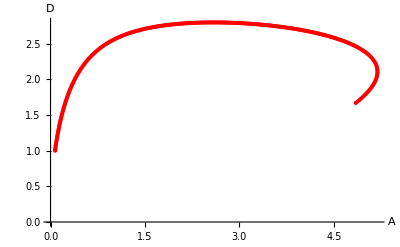

```mathematica
plotnumerique2=ListPlot[Data2,AxesLabel-> {Style["A",FontSize->22],Style["D",FontSize->22]},LabelStyle->{FontSize->22},AspectRatio->1/GoldenRatio,PlotStyle->Red]
```

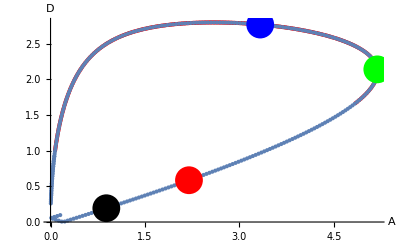

```mathematica
Show[plotnumerique2,plotnumerique,plotdot2,AxesStyle->Black,Epilog->{PointSize[0.05],Riffle[{Blue,Green,Red,Black},Point/@Datadots]}]
```